#### Plot admissible SU3 intertwiners in the P,Q plane

What is done here : 
1) Consider  the irreducible representation (irrep)  with highest weight (hw)  [1,1], written in the Dynkin basis (fundamental weights), ie, the adjoint representation.
2) Scale the highest weight by the positive integer s, ie consider the irrep [s, s].
3) Take the (tensor) square of [s,s] and decompose it on irreps with highest weights of components [la,mu].
4) Write the obtained [la,mu] as  extended partitions {la+mu, mu, 0}.
5) Perform a constant shift on such a partition in order to get ga = {ga1, ga2, ga3} with ga1+ga2+ga3 = 0.
6) Set P = ga1 ga2 + ga2 ga3 + ga3 ga1 and Q = - ga1 ga2 ga3
7) For each s, and each irrep [la,mu] appering in the decomposition of [s,s]^2 , plot the associate {P,Q} pair in the P, Q plane. Actually, in order to be able to plot and superimpose all these plots for distinct values of s, we rescale the obtained {P,Q} pairs as follows : {P,Q} --> {P/s^2, Q/s^3}.

The above description uses irreps of SU(3), but one could rephrased it in terms of Schur polynomials, or zonal polynomials, or Jack polynomials...  The ``multiplicities’’  (Littlewood-Richardson) would be different -- usually they are not  integers in the zonal case -- but we don’t use their values anyway here since we only draw one point for every term that appears. `

All the (rescaled) points {P,Q}  lie within the Horn curved polygon described in this article.

The “emergence” (when s increases) of new points in the P,Q plane is pictured by choosing smaller and smaller radii for the points.

The code for tensorprod should be evaluated first : use another notebook, for instance the file “Intertwiners&HoneycombsForSU3.nb” or  use  the more general code “Product of irreducible representations of SU(n) and decomposition into a direct sum”  available on the web page  
http://www.cpt.univ-mrs.fr/~coque/Computer_programs/index.html
If one only wants to look at the results, this is not needed (see below) :

```mathematica
br[n_]:=SortBy[Tally[tensorprod[{n,n},{n,n},{u,v}]],Last]
```

```mathematica
br[2]
```

{{{0,0},1},{{0,3},1},{{0,6},1},{{2,5},1},{{3,0},1},{{4,4},1},{{5,2},1},{{6,0},1},{{1,1},2},{{1,4},2},{{3,3},2},{{4,1},2},{{2,2},3}}

```mathematica
partitionToVP[{a_,b_,c_}]:= {a,b,c} - (a+b+c)/3 {1,1,1};
```

```mathematica
partitionToVP[{7,2,0}]
```

{4,-1,-3}

```mathematica
dynkinToVP[{l1_,l2_}]:=partitionToVP[{l1+l2,l2,0}]
```

```mathematica
dynkinToVP[{5,2}]
```

{4,-1,-3}

```mathematica
partitionToPQ[{a_,b_,c_}]:=With[{g1=partitionToVP[{a,b,c}][[1]],
g2=partitionToVP[{a,b,c}][[2]],g3=partitionToVP[{a,b,c}][[3]]},{g1 g2 + g2 g3 + g3 g1, -g1 g2 g3}](* same result
```

```mathematica
partitionToPQ[{7,2,0}]
```

{-13,-12}

```mathematica
partitionToPQ[{4,-1,-3}]
```

{-13,-12}

```mathematica
(* Remark :  partitionToPQ[{a,b,c}] == partitionToPQ[partitionToVP[{a,b,c}]] *)
```

```mathematica
test[n_]:=Map[partitionToPQ,Map[dynkinToVP,Map[First,br[n]]]]
```

```mathematica
partitionToPQ[dynkinToVP[{5,2}]]
```

{-13,-12}

```mathematica
test[1]
```

{{0,0},{-3,2},{-4,0},{-3,-2},{-1,0}}

```mathematica
test[2]
```

{{0,0},{-3,2},{-12,16},{-13,12},{-3,-2},{-16,0},{-13,-12},{-12,-16},{-1,0},{-7,6},{-9,0},{-7,-6},{-4,0}}

```mathematica
test[3]
```

{{0,0},{-3,2},{-12,16},{-27,54},{-28,48},{-3,-2},{-31,30},{-12,-16},{-36,0},{-31,-30},{-28,-48},{-27,-54},{-1,0},{-7,6},{-19,30},{-21,20},{-7,-6},{-25,0},{-21,-20},{-19,-30},{-4,0},{-13,12},{-16,0},{-13,-12},{-9,0}}

```mathematica
(* etc *)
```

```mathematica
plottest[n_]:=ListPlot[test[n]/ConstantArray[{n^2, n^3},Length[test[n]]],PlotStyle->{Thick,PointSize[0.030-0.004 (n-1)],ColorData[n,"ColorList"]}]
```

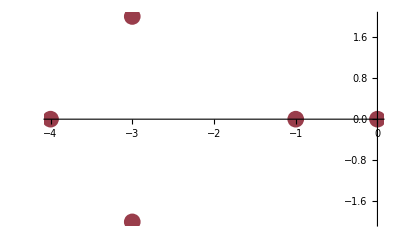

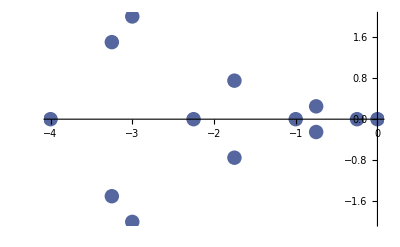

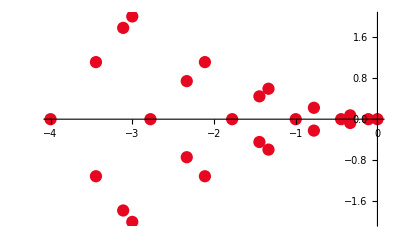

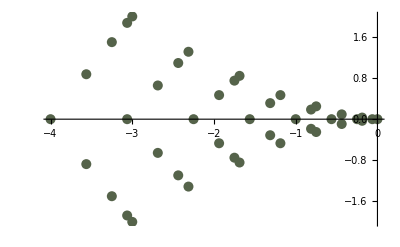

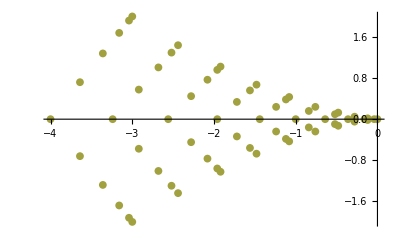

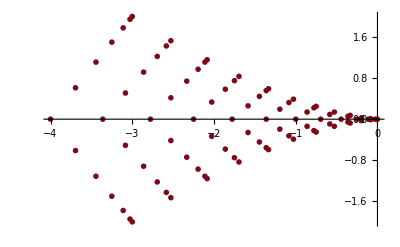

```mathematica
plottest[1]
plottest[2]
plottest[3]
plottest[4]
plottest[5]
plottest[6]
```

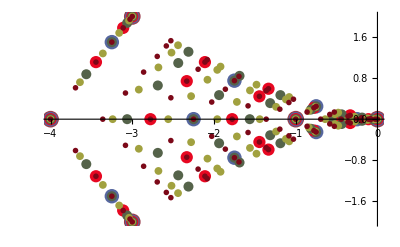

```mathematica
Show[plottest[1],plottest[2],plottest[3],plottest[4],plottest[5],plottest[6]]
```

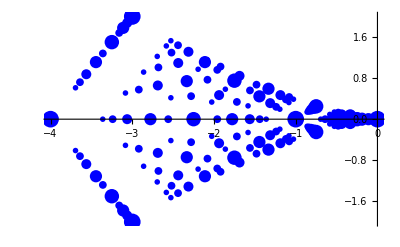

```mathematica
Show[plottest[1],plottest[2],plottest[3],plottest[4],plottest[5],plottest[6],PlotStyle->Directive[Opacity[0.2],Blue]]
```